```mathematica
SetDirectory[NotebookDirectory[]];
Needs["QuickErrorPlot`"]
```

```mathematica
data=Import["Example.xlsx"];
sheets=Import["Example.xlsx","Sheets"];
```

```mathematica
?QuickErrorPlot
?QuickFit
?QuickFitPlot
```

QuickErrorPlot[ data , <options> ]:
  Creates a simple ErrorListPlot with a Legend.

Data must contain exactly 4 columns - x, y, Δx, Δy, and must be
in a form of sheets: {{{x, y, Δx, Δy}, {...}, ...}, {...}, ...}

This is a list of options that QuickErrorPlot accepts and their
default options. Where multiple options are listed, the first 
is the default:

General:
    Legend           → {},
    LegendPosition   → {0.75, -0.3},
    RemoveLinesStart -> 0,
    RemoveLinesEnd   -> 0,
    Colors           → 1,
    ColorsStart      → 1,

For the Plot:
    Labels        → {"",""},
    Title         → "",
    PlotRange     → Automatic,
    AspectRatio   → 1/GoldenRatio

QuickFit[ data , <options> ]:
  Creates simple fits for data.

Data must contain exactly 4 columns - x, y, Δx, Δy, and must be
in a form of sheets: {{{x, y, Δx, Δy}, {...}, ...}, {...}, ...}

This is a list of options that QuickFit accepts and their
default options. Where multiple options are listed, the first 
is the default:

General:
    RemoveLinesStart -> 0,
    RemoveLinesEnd   -> 0

QuickFitPlot[ data , <options> ]:
  Creates simple fits for data and plot them.

Data must contain exactly 4 columns - x, y, Δx, Δy, and must be
in a form of sheets: {{{x, y, Δx, Δy}, {...}, ...}, {...}, ...}

This is a list of options that QuickFitPlot accepts and their
default options. Where multiple options are listed, the first 
is the default:

General:
    RemoveLinesStart -> 0,
    RemoveLinesEnd   -> 0,
    Colors           → 1,
    ColorsStart      → 1

For the Plot:
    Select -> All | {1, 2, ...},
    XRange → Automatic | {1, 2}

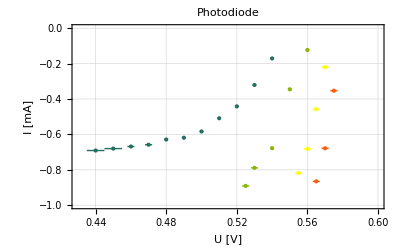

```mathematica
QuickErrorPlot[data,RemoveLinesStart->1,Legend->sheets,PlotRange->{{0.43,.6},{-1,0}},Labels->{"U [V]","I [mA]"},Title->"Photodiode",Colors->3,ColorsStart->2]
```

```mathematica
data2=Import["Example2.xlsx"];
```

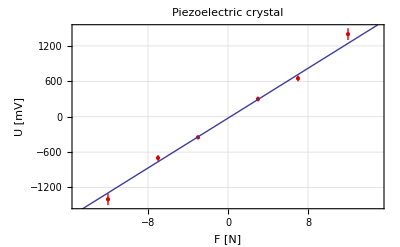

```mathematica
plot=QuickErrorPlot[data2,RemoveLinesStart->1,PlotRange->{{-15,15},{-1500,1500}},Labels->{"F [N]","U [mV]"},Title->"Piezoelectric crystal",Colors->2];
fplot=QuickFitPlot[data2,RemoveLinesStart->1,XRange->{-15,15}];
Show[plot, fplot]
```

```mathematica
fit=QuickFit[data2,RemoveLinesStart->1][[1]];
fit["BestFitParameters"]
fit["ParameterErrors"]
```

{-24.6137,105.63}

{19.2071,3.47424}